Note: In this problem set, expressions in green cells match corresponding expressions in the text answers.

4 - 8 Calculation of curl
Find curl v for v given with respect to right-handed Cartesian coordinates.

5.  v = x y z {x, y, z}

```mathematica
Clear["Global`*"]
```

```mathematica
e1=Curl[{x^2 y z,x y^2 z,x y z^2},{x,y,z}]
```

{-x y^2+x z^2,x^2 y-y z^2,-x^2 z+y^2 z}

7.  v={0, 0, ⅇ^-x Sin[y]}

```mathematica
Clear["Global`*"]
```

```mathematica
e1=Curl[{0,0,ⅇ^-x Sin[y]},{x,y,z}]
```

{ⅇ^-x Cos[y],ⅇ^-x Sin[y],0}

9 - 13 Fluid flow
Let v be the velocity vector of a steay fluid flow. Is the flow irrotational? Incompressible? Find the streamlines (the paths of the particles.) Hint. See the answers to problems 9 and 11 for a determination of a path.

9.  v={0,3 z^2,0}

```mathematica
Clear["Global`*"]
```

```mathematica
e1=Div[{0,3 z^2,0},{x,y,z}]
```

0

The divergence being zero means that the flow is incompressible, by numbered line (7) on p. 405.

```mathematica
e2=Curl[{0,3 z^2,0},{x,y,z}]
```

{-6 z,0,0}

Example 3, p. 408 says that if the flow is irrotational, the curl should be zero. The curl of the present function is not zero, so it is rotational.

```mathematica
e3=DSolve[3 z^2==y'[z],y,z]
```

{{y→Function[{z},z^3+C[1]]}}

The solution to e3 is possibly the flow function, but I think direction fields and streamplots are about differential equations. The streamplot below gives an impression of bending flow, but is that rotational?

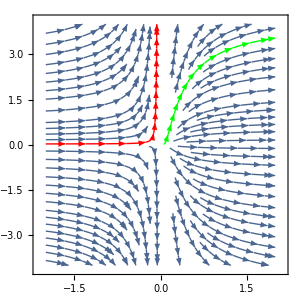

```mathematica
StreamPlot[{3 z^2,y},{z,-2,2},{y,-4,4},StreamPoints->{{{{1,3},Green},{{-.2,.12},Red},Automatic}},ImageSize->300]
```

11.  v = {y, -2 x, 0}

```mathematica
Clear["Global`*"]
```

```mathematica
e1=Div[{y,-2 x,0},{x,y,z}]
```

0

The divergence being zero means that the flow is incompressible, by (7) on p. 405.

```mathematica
e2=Curl[{y,-2 x,0},{x,y,z}]
```

{0,0,-3}

The curl not being zero implies it is rotational.

```mathematica
e3=DSolve[-2x==y'[x],y,x]
```

{{y→Function[{x},-x^2+C[1]]}}

```mathematica
e4=DSolve[y==x'[y],x,y]
```

{{x→Function[{y},y^2/2+C[1]]}}

With an expression of x in the y slot and an expression of y in the x slot, it might make for a plot that is both shaken and stirred. Just as a speculation, I’ll look at the following. I’m not sure this could be called rotational either.

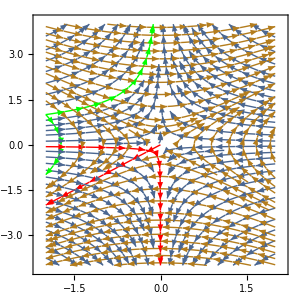

```mathematica
StreamPlot[{{-2x,y},{y,x}},{x,-2,2},{y,-4,4},StreamPoints->{{{{-2,1},Green},{{-.2,-.2},Red},Automatic}},ImageSize->300]
```

Looking at the text answer, I see that it may be possible to consolidate the equation. I have

x' = y  and y' = -2 x ⇒ y' + 2 x = 0 ⇒ y' y + 2 x' x = 0

Integrating in hopscotch pattern, I can come up with x^2+1/2 y^2=c, and though it’s not the differential form, I can still try plotting.

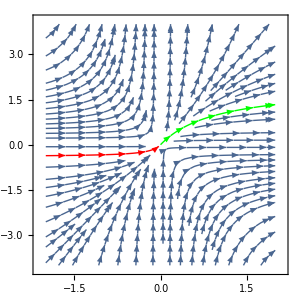

```mathematica
StreamPlot[{x^2,y^2/2},{x,-2,2},{y,-4,4},StreamPoints->{{{{1,1},Green},{{-.2,-.2},Red},Automatic}},ImageSize->300]
```

13.  v = {x, y, -z}

```mathematica
Clear["Global`*"]
```

```mathematica
e1=Div[{x,y,-z},{x,y,z}]
```

1

The divergence being nonzero means that the flow is compressible, by (7) on p. 405.

```mathematica
e2=Curl[{x,y,-z},{x,y,z}]
```

{0,0,0}

The curl being zero implies it is irrotational.

15 - 20 Div and curl
With respect to right-handed coordinates, let u={y, z, x}, v = {yz, zx, xy}, f = x y z, and g = x + y + z. Find the given expressions. Check your result by a formula in project 14 if applicable.

15. curl (u + v), curl v

```mathematica
Clear["Global`*"]
```

```mathematica
e1=uu[x_,y_,z_]={y,z,x}
```

{y,z,x}

```mathematica
e2=vv[x_,y_,z_]={y z,z x,x y}
```

{y z,x z,x y}

```mathematica
e3=ff[x_,y_,z_]=x y z
```

x y z

```mathematica
e4=gg[x_,y_,z_]=x+y+z
```

x+y+z

```mathematica
e5=Curl[uu[x,y,z]+vv[x,y,z],{x,y,z}]
```

{-1,-1,-1}

```mathematica
e6=Curl[vv[x,y,z],{x,y,z}]
```

{0,0,0}

Above: in the text answer, e5 and e6 were supposed to come out the same. Why didn’t they?

```mathematica
e66=Curl[uu[x,y,z],{x,y,z}]
```

{-1,-1,-1}

Above: Possible typo alert. Perhaps the problem description was meant to read “curl u” instead of “curl v”.

17.  v.curl u, u.curl v, u.curl u

```mathematica
e9=vv[x,y,z].Curl[uu[x,y,z],{x,y,z}] (* text answer = -yz -zx -xy *)
```

```mathematica
-x y-x z-y z
```

The above answer, e9, does not match the text answer. However, I assume that x, y, and z are real numbers, and therefore due to real commutativity, they should be equal to the text answer.

```mathematica
e10=uu[x,y,z].Curl[vv[x,y,z],{x,y,z}]
```

0

```mathematica
e11=uu[x,y,z].Curl[uu[x,y,z],{x,y,z}] (* text answer = -y -z -x *)
```

```mathematica
-x-y-z
```

Above: Green invoked by commutativity principle for reals.

19.  curl (gu + v), curl (gu)

```mathematica
e12=Curl[gg[x,y,z] uu[x,y,z]+vv[x,y,z],{x,y,z}]
```

{-y-2 z,-2 x-z,-x-2 y}

```mathematica
e13=Curl[gg[x,y,z] uu[x,y,z],{x,y,z}]
```

{-y-2 z,-2 x-z,-x-2 y}